# Rescaled f(R) Canonical Scalar Field Inflation In The Presence Of A Gauβ-Bonnet Term.

## Error functions as the Gauβ-Bonnet scalar Coupling function.

### 1. Designation of scalar coupling function-Solution of continuity equation

We start by designating the scalar functions of the model. For simplicity, the Gauβ-Bonnet scalar coupling function is assume to be the error function such that the ratio of the first two derivatives of the scalar functions, which plays an important role in the constrained Gauβ-Bonnet model as shown in arXiv:2003.13724, is simplified greatly. Now the form of the scalar potential is extracted from the continuity equation of the scalar field by treating it as a first order differential equation with respect to the scalar potential. The equations of motion are extracted by assuming the slow-roll condition is valid. Slow-roll indices along with observed indices are taken from arXiv:0412126.

Every parameter that ends with 0 or 1 is an auxiliary free parameter that needs to be designated later or is used as an intermediate state. With ξ and V the Gauβ-Bonnet scalar coupling and the scalar potential are denoted while H is Hubble's parameter and H2 the squared Hubble. Each parameter ending with dot implies time derivative for simplicity and E0, Qa, Qe, Qt are auxiliary function that depend solely on  the scalar field. Finally, indices ε1 through ε4 are the slow-roll indices of the model and ns, nt, r indicate the observed indices.

```mathematica
ξ[φ_]:=λ Erf[γ (κ φ)];
H20[φ_]=κ^2 V0[φ]/(3α);
difeq1=D[V0[φ],φ]+3H20[φ]ξ'[φ]/ξ''[φ]+24D[ξ[φ],φ]H20[φ]^2;
s=DSolve[difeq1==0,V0[φ],φ];
```

```mathematica
V[φ_]:=V0[φ]/.s[[1]]/.C[1]->V1
```

The proper functions depending on the potential are specified here

```mathematica
H2[φ_]:=κ^2 V[φ]/(3α)
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=H[φ]ξ'[φ]/ξ''[φ];
Hdot[φ_]:=-κ^2 φdot[φ]^2/(2α)
ξdot[φ_]:=ξ'[φ]φdot[φ];
```

### 2. Auxiliary Functions

We know specify the auxiliary parameters that are needed in order to simplify computations.

```mathematica
Qa[φ_]:=-8ξdot[φ]H2[φ]
Qt[φ_]:=α/κ^2-8ξdot[φ]H[φ]
Qe[φ_]:=-32ξdot[φ]Hdot[φ]
E0[φ_]:=α/κ^2(1+3 Qa[φ]^2/(2Qt[φ]*φdot[φ]^2))
E0dot[φ_]:=D[E0[φ],φ]φdot[φ]
Qtdot[φ_]:=D[Qt[φ],φ]φdot[φ]
```

### 3. Slow-roll Indices

In this section, the slow-roll indices are defined.

```mathematica
ε1[φ_]:=1/(2α)(κ ξ'[φ]/ξ''[φ])^2
ε2[φ_]:=1-ε1[φ]-ξ'[φ]ξ'''[φ]/ξ''[φ]^2
ε3[φ_]:=E0dot[φ]/(2H[φ]E0[φ])
ε4[φ_]:=Qtdot[φ]/(2H[φ]Qt[φ])
```

### 4. Observed Indices

Here, the observables which shall be computed during the first horizon crossing are specified. The sound wave velocity is included not only due to the tensor to scalar ratio but to also analyse whether the model is free of ghost instabilities due to the Gauβ-Bonnet scalar coupling functions which is assumed to be dynamical and not constant.

```mathematica
nS[φ_]:=1-2(2ε1[φ]+ε2[φ]+ε3[φ])
CA[φ_]:=Sqrt[1+(Qa[φ]Qe[φ])/(2φdot[φ]^2Qt[φ]+3Qa[φ]^2)]
r[φ_]:=16Abs[(α ε1[φ]-κ^2Qe[φ]/(4H[φ])) CA[φ]^3/(κ^2Qt[φ])]
nT[φ_]:=-2(ε1[φ]+ε4[φ])
```

### 5. Initial and Final Value of the scalar field

To study the inflationary era, one needs to insert as an input the value of the scalar field during the first horizon crossing to the observed indices. Such a value can be extracted by firstly finding the final value during the ending stage of the inflationary era by imposing that ε1 becomes of order O(1). Afterwards, by using the e-folding number N=∫ Hdt, the initial value can be extracted as a function of N and φf.

```mathematica
U1=Solve[ε1[φ]==1,φ];
φf=φ/.U1[[2]];
U2a=Integrate[ξ''[φ]/ξ'[φ],φ]/.φ->φl;
U2b=Integrate[ξ''[φ]/ξ'[φ],φ]/.φ->φk;
U3=Solve[N0==U2a-U2b,φk];
φi=φk/.U3[[2]]/.{φl->φf} /.C[1]->0;
```

### 6. Numerical Results

By assigning numerical values to the free parameters of the model, the initial value of the scalar field during the first horizon crossing is extracted. Subsequently, one can use such value as an input on the observed indices and derive results.

```mathematica
κ=1;N0=60;λ=-1;V1=11. 10^(-21);α=0.004;γ=12;
φi//N
φf//N
nS[φ]/.φ->φi//N
r[φ]/.φ->φi//N
nT[φ]/.φ->φi//N
CA[φ]/.φ->φi//N
φf-φi//N
D[V[φ],φ]/V[φ]/.φ->φi//N
-D[V[φ],{φ,2}]/V[φ]/.φ->φi//N
```

0.646664

0.0388206

0.964659

0.0576594

-0.00191182

0.999986

-0.607843

2.32758

177.851

### 7. Approximations- String Corrections

At this stage we ascertain whether the slow-roll conditions are valid. The results should be compared at pairs of two where the first must be smaller than the second by 2-3 orders at least.

```mathematica
Hdot[φ]/.φ->φi//N
H2[φ]/.φ->φi//N
1/2 φdot[φ]^2/.φ->φi//N
V[φ]/.φ->φi//N
D[φdot[φ],φ]/.φ->φi//N
3*H[φ]*φdot[φ]/.φ->φi//N
```

-1.86017×10^19

5.16159×10^21

7.44066×10^16

6.19391×10^19

1.47597×10^8

-8.31445×10^19

These are the terms that were absent from the equations of motion and are compared with the terms which were kept exactly as in the previous case.

```mathematica
24D[ξ[φ],φ] H2[φ]^2/.φ->φi//N
D[V[φ],φ]/.φ->φi//N
16*ξdot[φ]H[φ]Hdot[φ]/.φ->φi//N
Hdot[φ]/.φ->φi//N
24*ξdot[φ]*H[φ]*H2[φ]/.φ->φi//N
3H2[φ]/.φ->φi//N
```

-6.10235×10^19

1.44168×10^20

-7.87233×10^14

-1.86017×10^19

3.27662×10^17

1.54848×10^22

### 8. Numerical values of slow-roll indices

The numerical value of the slow-roll indices in general suffices in order to ascertain the validity of the slow-roll conditions.

```mathematica
ε1[φ]/.φ->φi//N
ε2[φ]/.φ->φi//N
ε3[φ]/.φ->φi//N
ε4[φ]/.φ->φi//N
```

0.00360386

0.00469944

0.0057635

-0.00264795

### 9. Diagrammatic representation of the observed indices

Here we showcase the area of viability of the observed indices for specific set of parameters.

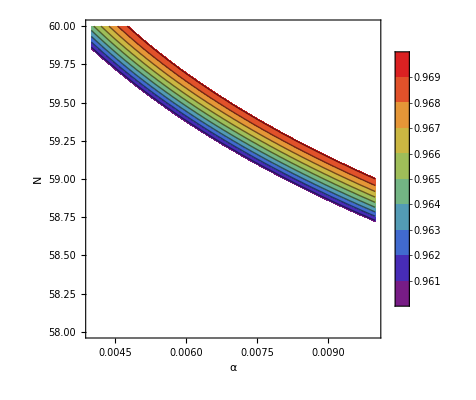

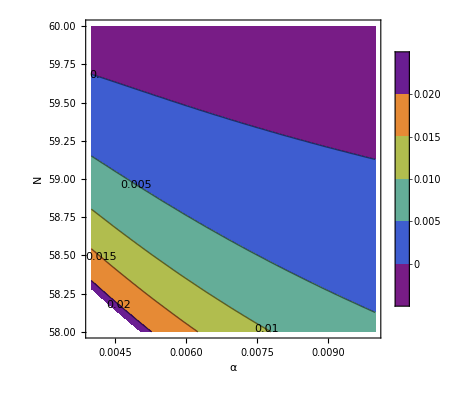

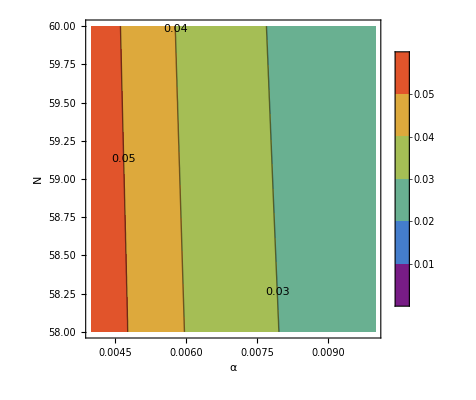

```mathematica
Clear[N0];Clear[α]
ContourPlot[Evaluate[nS[φ]/.φ->φi],{α,0.004,0.01},{N0,58.,60.},PlotLegends->True,FrameLabel->{"α","N"}, PlotRange->{0.9607, 0.9691},ColorFunction->{"Rainbow"}]
ContourPlot[Evaluate[nT[φ]/.φ->φi],{α,0.004,0.01},{N0,58.,60.},PlotLegends->True,FrameLabel->{"α","N"},ColorFunction->{"Rainbow"},ContourLabels->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{α,0.004,0.01},{N0,58.,60.},PlotLegends->True,FrameLabel->{"α","N"}, PlotRange->{0, 0.064},ColorFunction->{"Rainbow"},ContourLabels->True]
```

### 10. Viability of Swampland criteria

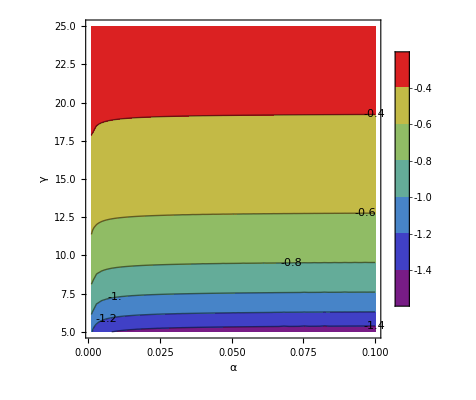

```mathematica
N0=60; 
Clear[λ,α,n,γ];
n=4;
κ=1;
λ=-1;
Δφ=φf-φi;
ContourPlot[Δφ,{α,0.001,0.1},{γ,5,25},FrameLabel->{"α","γ"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

2.32758

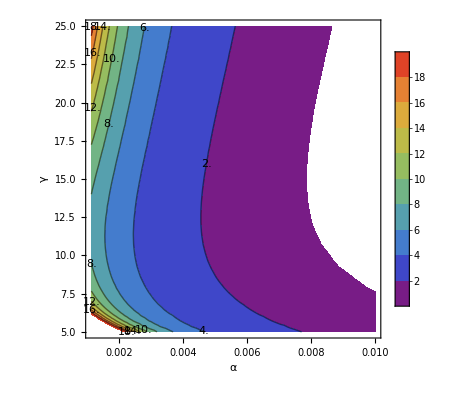

```mathematica
Evaluate[D[V[φ], φ]/V[φ] /. φ -> φi] /. {γ -> 12, 
  α -> 0.004} (* satisfied*)
ContourPlot[
 Evaluate[D[V[φ], φ]/V[φ] /. φ -> φi], {α, 0.00112, 0.01}, {γ, 5, 25}, 
 FrameLabel -> {"α", "γ"}, 
 ContourLabels -> All, PlotLegends -> Automatic, 
 ColorFunction -> "Rainbow", PlotRange -> {1, 20}]
```

177.851

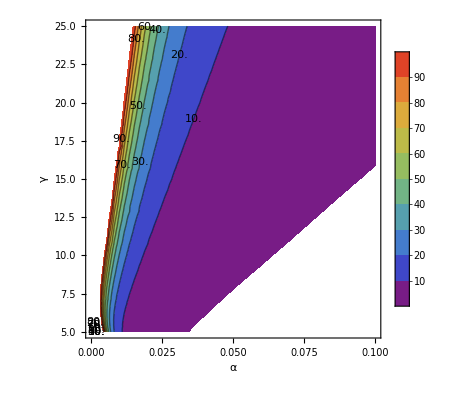

```mathematica
Evaluate[-D[V[φ],{φ,2}]/V[φ] /. φ -> φi] /. {γ -> 12, 
  α -> 0.004} (*NOT satisfied*)
ContourPlot[
 Evaluate[-D[V[φ],{φ,2}]/V[φ] /. φ -> φi], {α, 0.001, 0.1}, {γ, 5, 25}, 
 FrameLabel -> {"α", "γ"}, 
 ContourLabels -> All, PlotLegends -> Automatic, 
 ColorFunction -> "Rainbow", PlotRange -> {1, 100}]
```